```mathematica
(*with rfd, 5000 non interacting particles*)
SetDirectory[NotebookDirectory[]];
dir="/home/drladiges/gigan/projects/FHDeX/exec/";
(*dir="/home/drladiges/gigan/projects/FHDeX/exec/";*)
file="asciiVx000035000";
count=2;
slist={"E","F"};
(*slist={"E","F","G","H"};*)(*eo damp 0*)
(*slist={"I","J","K","L"};*)(*eo wet 120*)
(*slist={""};*)
rawList=Table[0,{ii,1,count}];
(*dir="/home/drladiges/projects/FHDeX/exec/";.
file="ascii_means000000150";*)

For[kk=1,kk≤count,kk++,
raw0=Import[dir<>"immersedIons"<>slist[[kk]]<>"/0_"<>file,"Table"];
raw1=Import[dir<>"immersedIons"<>slist[[kk]]<>"/1_"<>file,"Table"];
raw2=Import[dir<>"immersedIons"<>slist[[kk]]<>"/2_"<>file,"Table"];
raw3=Import[dir<>"immersedIons"<>slist[[kk]]<>"/3_"<>file,"Table"];
raw4=Import[dir<>"immersedIons"<>slist[[kk]]<>"/4_"<>file,"Table"];
raw5=Import[dir<>"immersedIons"<>slist[[kk]]<>"/5_"<>file,"Table"];
raw6=Import[dir<>"immersedIons"<>slist[[kk]]<>"/6_"<>file,"Table"];
raw7=Import[dir<>"immersedIons"<>slist[[kk]]<>"/7_"<>file,"Table"];
(*rawA=Join[raw0[[1;;-3]],raw1[[1;;-3]],raw2[[1;;-3]],raw3[[1;;-3]]];*)
rawA=Join[raw0[[1;;-3]],raw1[[1;;-3]],raw2[[1;;-3]],raw3[[1;;-3]],raw4[[1;;-3]],raw5[[1;;-3]],raw6[[1;;-3]],raw7[[1;;-3]]];
rawList[[kk]]=rawA/.{}->Nothing;
];
```

```mathematica
xsize=128;
ysize=128;
zsize=64;
(*xsize=64;
ysize=64;
zsize=32;*)
cell=1;

func3D=Table[0,{ii,1,count}];
func2D=Table[0,{ii,1,count}];

For[ll=1,ll≤count,ll++,
members3DA=Table[{ToExpression[StringReplace[rawList[[ll,ii,1]],{"("-> "{",")"-> "}"}]],rawList[[ll,ii,2]]},{ii,1,Length[rawList[[ll]]]}];
members3DA= DeleteDuplicatesBy[members3DA,First];
func3D[[ll]]=Interpolation[members3DA,InterpolationOrder->0];
membersFlat=Flatten[Table[{{ii,jj},Mean[Table[func3D[[ll]][ii,jj,kk],{kk,0,zsize-1,cell}]]},{ii,0,xsize-1},{jj,0,ysize-1}],1];
func2D[[ll]]=Interpolation[membersFlat,InterpolationOrder->0];
];
```

```mathematica
func2DM[x_,y_] = Sum[func2D[[ll]][x,y],{ll,1,count}]/count;
```

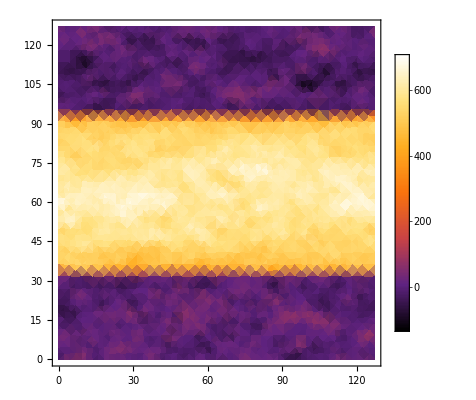

```mathematica
DensityPlot[func2DM[x,y],{x,0,xsize-1},{y,0,ysize-1},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

```mathematica
membersFlatter=Flatten[Table[{{jj,Mean[Table[func2DM[ii,jj],{ii,0,xsize-1,cell}]]}},{jj,0,ysize-1}],1];
func1DM=Interpolation[membersFlatter,InterpolationOrder->1];
```

```mathematica
(*size=8.284925963482451*10^-7;*)
size=13.06*10^-7;
dx=size/xsize;
posFunc[x_]=x/dx -0.5;


m1=Graphics[{Thick,Red,Circle[{0,0},1]}];
m2=Graphics[{Thick,Black,Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}];
m3=Graphics[{Thick,Purple,Line[{{-0.5,-0.5},{0.5,0.5}}],Line[{{-0.5,0.5},{0.5,-0.5}}]}];
m4=Graphics[{Thick,Green,Line[{{0,-0.5},{-0.5,0},{0,0.5},{0.5,0},{0,-0.5}}]}];

ml1=Graphics[Line[{{0.25size,-20},{0.25size,900}}]];
ml2=Graphics[Line[{{0.75size,-20},{0.75size,900}}]];
```

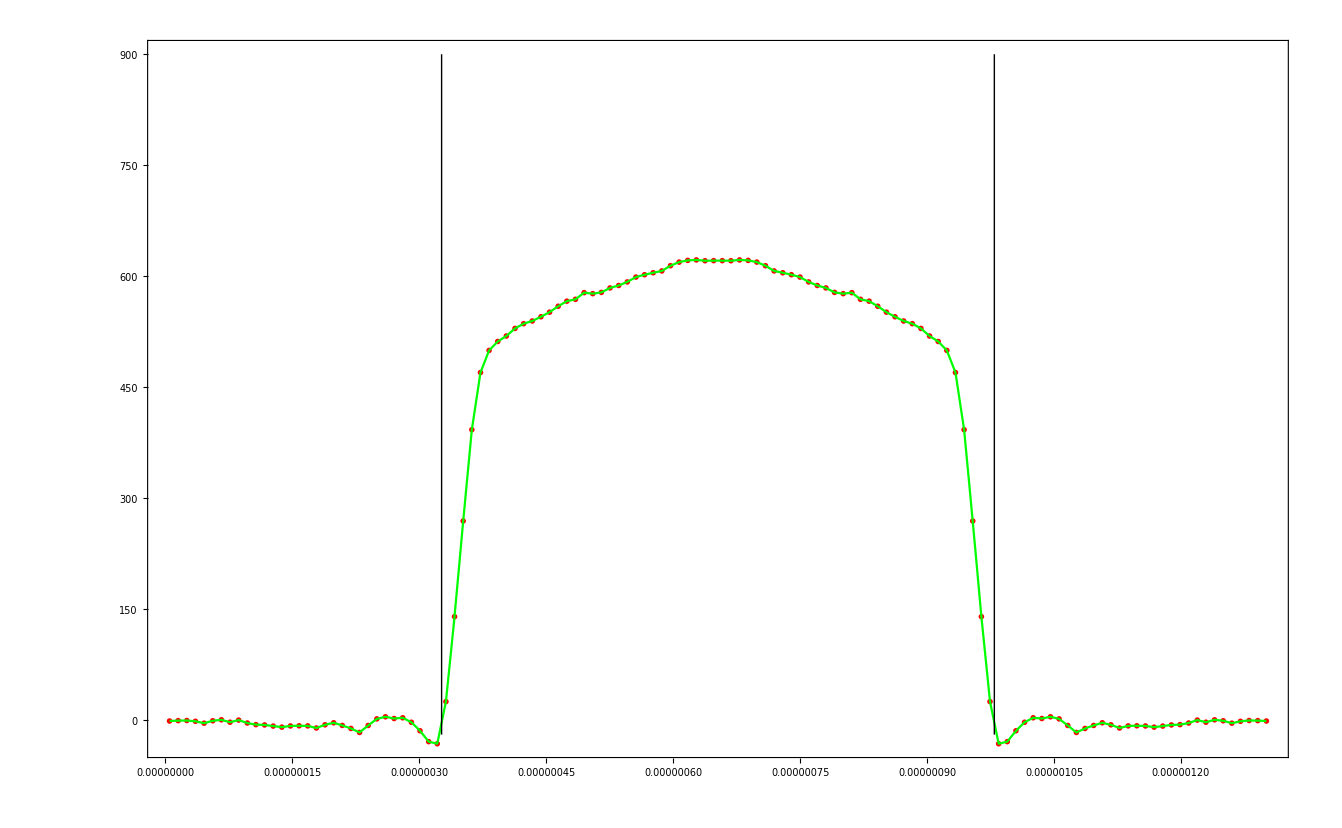

```mathematica
pa=ListPlot[Table[{y,(func1DM[posFunc[size-y]]+func1DM[posFunc[y]])/2},{y,dx/2,size-dx/2,dx}],PlotStyle->Red,PlotMarkers->{m4,0.03}];
pb=Plot[(func1DM[posFunc[size-y]]+func1DM[posFunc[y]])/2,{y,dx/2,size-dx/2},PlotRange->All,PlotStyle->Green];
Show[pa,pb,ml1,ml2,PlotRange->All,Frame->True,Axes->True]
```

```mathematica
func1DM[posFunc[size/2]]
```

875.266

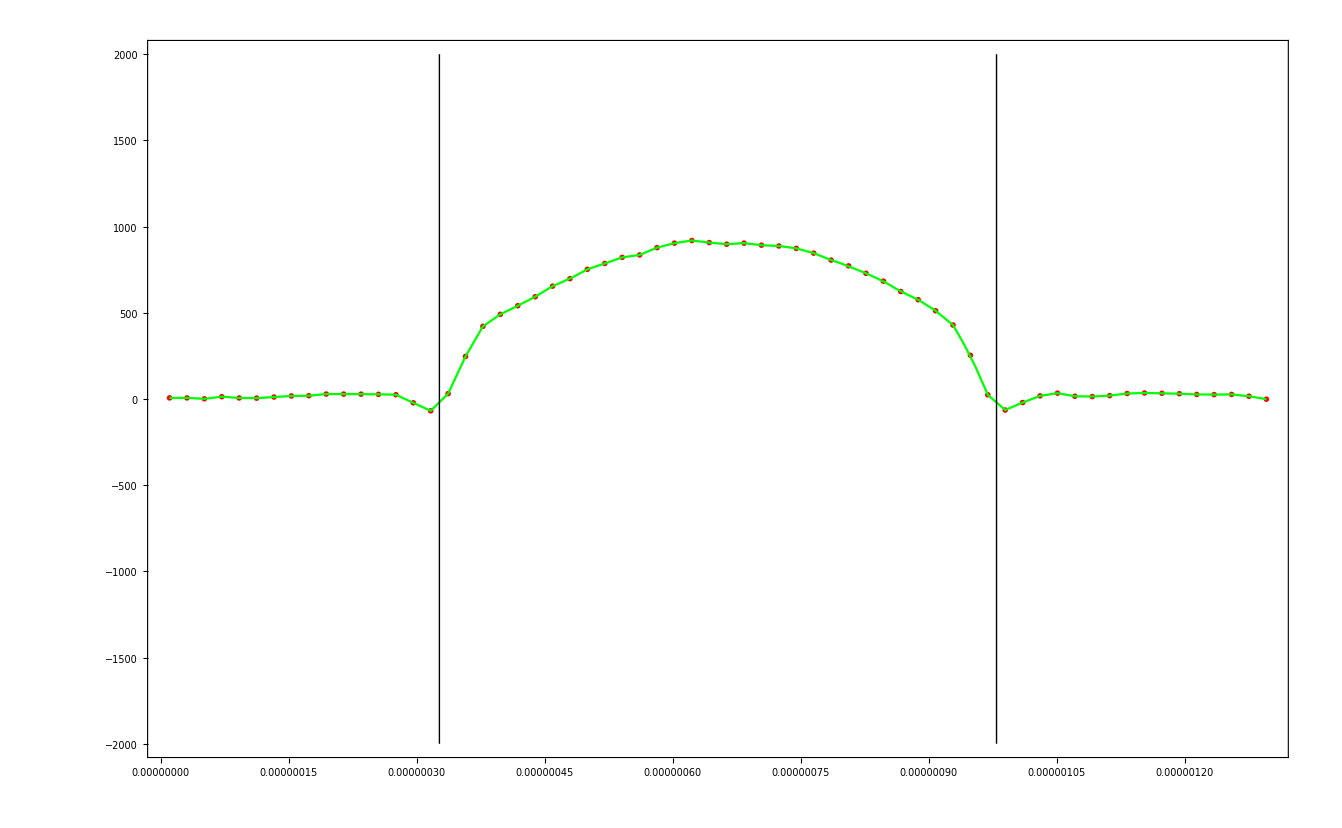

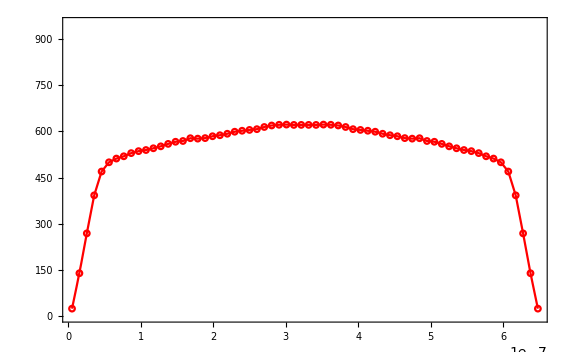

```mathematica
pa=ListPlot[Table[{y,(func1DM[posFunc[size-(y+0.25size)]]+func1DM[posFunc[(y+0.25size)]])/2},{y,dx/2,0.5size-dx/2,dx}],PlotMarkers->{m1,0.03},PlotRange->{0,900}];
pb=Plot[(func1DM[posFunc[size-(y+0.25size)]]+func1DM[posFunc[y+0.25size]])/2,{y,dx/2,0.5size-dx/2},PlotStyle->Red,PlotRange->{0,900}];
Show[pa,pb,Frame->True,Axes->False,AxesOrigin->{0,0},PlotRange->{0,950}]
```

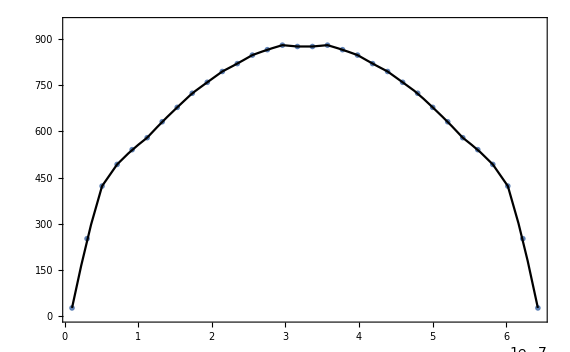
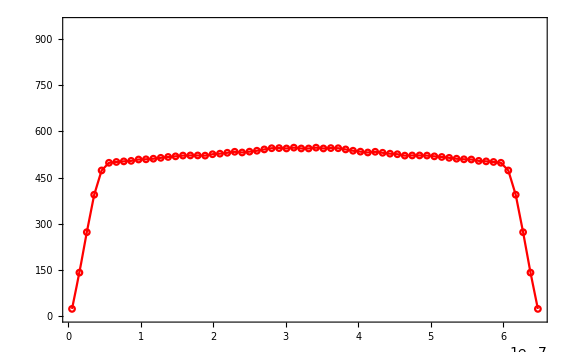
```mathematica
flow50=-Graphics-;
flow100=-Graphics-;
```

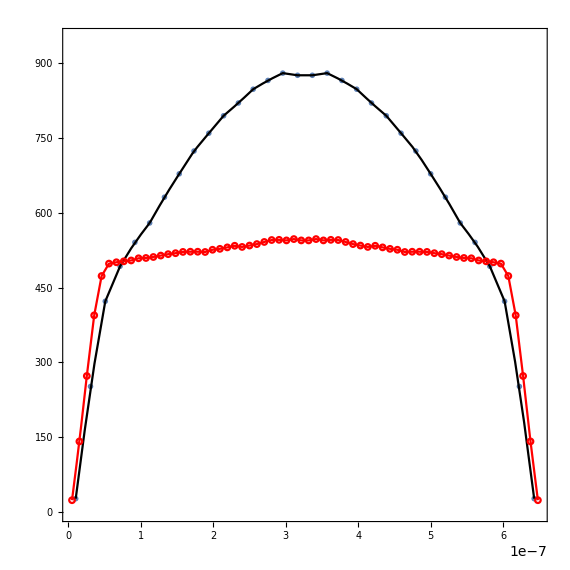

```mathematica
Show[flow50,flow100,AspectRatio->1]
```